```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hpgen300,hpgen800,hpgen1400,hp300keep,hp800keep,hp1400keep,hp300mem,hp800mem,hp1400mem,hpkill300,hpkill800,hpkill1400}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hp500c24htest.mx"];
```

```mathematica
{hptyp400,hptyp500,hptyp600,hptyp700,hptyp900,hptyp1000,hptyp1100,hptyp1200,hptyp1300}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hptyp.mx"];
```

```mathematica
{hptyp300,hptyp800,hptyp1400}=Parallelize[{titeryieldproductivity[hpkill300],titeryieldproductivity[hpkill800],titeryieldproductivity[hpkill1400]}];
```

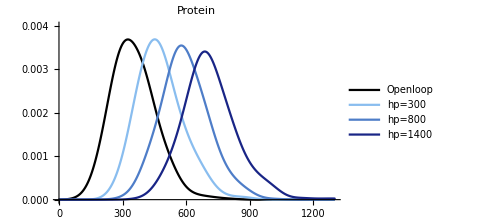

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hpgen300[[1]][[1]]/hpgen300[[1]][[6]],hpgen800[[1]][[1]]/hpgen800[[1]][[6]],hpgen1400[[1]][[1]]/hpgen1400[[1]][[6]]},50,PlotRange->{{0,1300},{0,0.004}},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

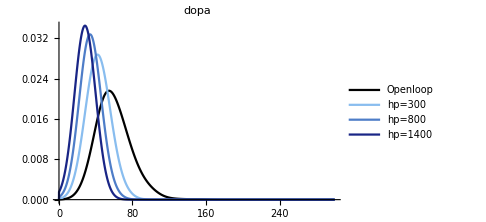

```mathematica
SmoothHistogram[{ol500c24h[[1]][[3]]/ol500c24h[[1]][[6]],hpgen300[[1]][[3]]/hpgen300[[1]][[6]],hpgen800[[1]][[3]]/hpgen800[[1]][[6]],hpgen1400[[1]][[3]]/hpgen1400[[1]][[6]]},10,PlotRange->{{0,300},Automatic},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["dopa",Black,16],
PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

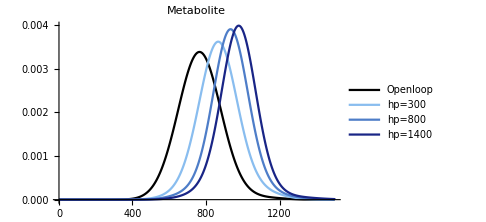

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hpgen300[[1]][[4]]/hpgen300[[1]][[6]],hpgen800[[1]][[4]]/hpgen800[[1]][[6]],hpgen1400[[1]][[4]]/hpgen1400[[1]][[6]]},80,PlotRange->{{0,1500},Automatic},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["Metabolite",Black,16],
PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

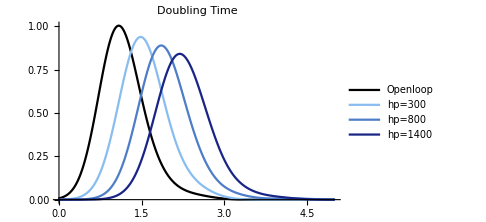

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hpgen300[[1]][[5]],Log[2]/hpgen800[[1]][[5]],Log[2]/hpgen1400[[1]][[5]]},0.3,PlotRange->{{0,5},Automatic},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

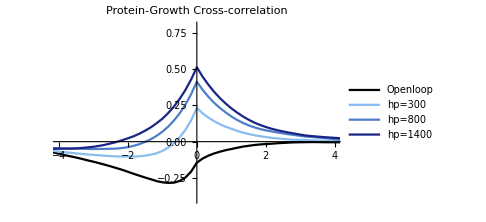

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hp300mem[[4]],hp800mem[[4]],hp1400mem[[4]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

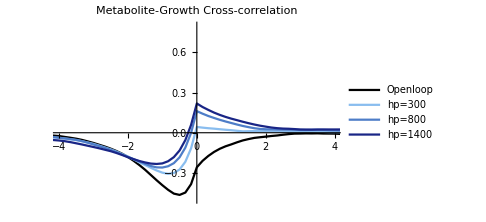

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hp300mem[[5]],hp800mem[[5]],hp1400mem[[5]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","hp=300","hp=800","hp=1400"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#89bdef"],Thick],Directive[RGBColor["#4e7dc8"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

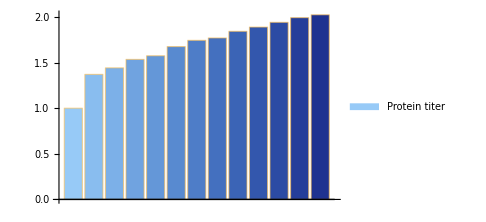

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hptyp300[[2]]/oltyp[[2]],hptyp400[[2]]/oltyp[[2]],hptyp500[[2]]/oltyp[[2]],hptyp600[[2]]/oltyp[[2]],hptyp700[[2]]/oltyp[[2]],hptyp800[[2]]/oltyp[[2]],hptyp900[[2]]/oltyp[[2]],hptyp1000[[2]]/oltyp[[2]],hptyp1100[[2]]/oltyp[[2]],hptyp1200[[2]]/oltyp[[2]],hptyp1300[[2]]/oltyp[[2]],hptyp1400[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#89bdef"],
RGBColor["#7cb0e8"],
RGBColor["#70a3e0"],
RGBColor["#6497d8"],
RGBColor["#588ad0"],
RGBColor["#4e7dc8"],
RGBColor["#4470bf"],
RGBColor["#3b64b6"],
RGBColor["#3357ad"],
RGBColor["#2c4ba4"],
RGBColor["#253e9a"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

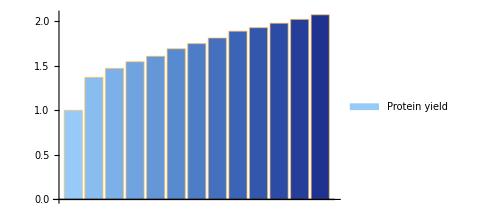

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hptyp300[[5]]/oltyp[[5]],hptyp400[[5]]/oltyp[[5]],hptyp500[[5]]/oltyp[[5]],hptyp600[[5]]/oltyp[[5]],hptyp700[[5]]/oltyp[[5]],hptyp800[[5]]/oltyp[[5]],hptyp900[[5]]/oltyp[[5]],hptyp1000[[5]]/oltyp[[5]],hptyp1100[[5]]/oltyp[[5]],hptyp1200[[5]]/oltyp[[5]],hptyp1300[[5]]/oltyp[[5]],hptyp1400[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#89bdef"],
RGBColor["#7cb0e8"],
RGBColor["#70a3e0"],
RGBColor["#6497d8"],
RGBColor["#588ad0"],
RGBColor["#4e7dc8"],
RGBColor["#4470bf"],
RGBColor["#3b64b6"],
RGBColor["#3357ad"],
RGBColor["#2c4ba4"],
RGBColor["#253e9a"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

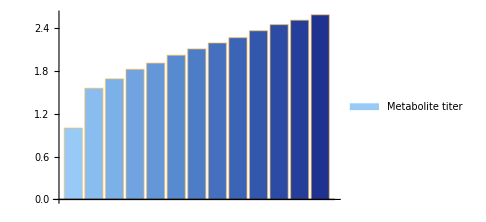

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hptyp300[[4]]/oltyp[[4]],hptyp400[[4]]/oltyp[[4]],hptyp500[[4]]/oltyp[[4]],hptyp600[[4]]/oltyp[[4]],hptyp700[[4]]/oltyp[[4]],hptyp800[[4]]/oltyp[[4]],hptyp900[[4]]/oltyp[[4]],hptyp1000[[4]]/oltyp[[4]],hptyp1100[[4]]/oltyp[[4]],hptyp1200[[4]]/oltyp[[4]],hptyp1300[[4]]/oltyp[[4]],hptyp1400[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#89bdef"],
RGBColor["#7cb0e8"],
RGBColor["#70a3e0"],
RGBColor["#6497d8"],
RGBColor["#588ad0"],
RGBColor["#4e7dc8"],
RGBColor["#4470bf"],
RGBColor["#3b64b6"],
RGBColor["#3357ad"],
RGBColor["#2c4ba4"],
RGBColor["#253e9a"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

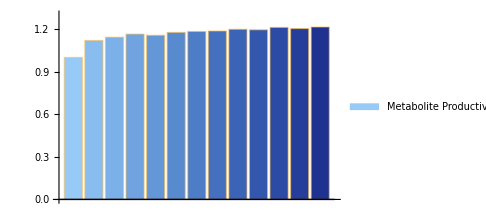

```mathematica
BarChart[{oltyp[[1]],hptyp300[[1]],hptyp400[[1]],hptyp500[[1]],hptyp600[[1]],hptyp700[[1]]/oltyp[[1]],hptyp800[[1]],hptyp900[[1]],hptyp1000[[1]],hptyp1100[[1]]/oltyp[[1]],hptyp1200[[1]]/oltyp[[1]],hptyp1300[[1]],hptyp1400[[1]]},PlotRange->{0,1.3},ChartLegends->{"Metabolite Productivity"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#89bdef"],
RGBColor["#7cb0e8"],
RGBColor["#70a3e0"],
RGBColor["#6497d8"],
RGBColor["#588ad0"],
RGBColor["#4e7dc8"],
RGBColor["#4470bf"],
RGBColor["#3b64b6"],
RGBColor["#3357ad"],
RGBColor["#2c4ba4"],
RGBColor["#253e9a"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[3]],hptyp300[[3]],hptyp400[[3]],hptyp500[[3]],hptyp600[[3]],hptyp700[[3]],hptyp800[[3]],hptyp900[[3]],hptyp1000[[3]],hptyp1100[[3]],hptyp1200[[3]],hptyp1300[[3]],hptyp1400[[3]]},PlotRange->Automatic,PlotLegends->{"Metabolite titer"},PlotStyle->{Black,
RGBColor["#89bdef"],
RGBColor["#7cb0e8"],
RGBColor["#70a3e0"],
RGBColor["#6497d8"],
RGBColor["#588ad0"],
RGBColor["#4e7dc8"],
RGBColor["#4470bf"],
RGBColor["#3b64b6"],
RGBColor["#3357ad"],
RGBColor["#2c4ba4"],
RGBColor["#253e9a"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-

# PERCENT

```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
{hpgen1,hpgen10,hpgen50,hpgen90,hpgen99,hpkeep1,hpkeep10,hpkeep50,hpkeep90,hpkeep99,hpmem1,hpmem10,hpmem50,hpmem90,hpmem99,hpkill1,hpkill10,hpkill50,hpkill90,hpkill99,hptyp1,hptyp10,hptyp50,hptyp90,hptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hp500c24hpercent.mx"];
```

```mathematica
{hpgen3000,hpgen6000,hmugen7000,hmugen14000,hpkeep3000,hpkeep6000,hmukeep7000,hmukeep14000,hpkill3000,hpkill6000,hmukill7000,hmukill14000}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hphmularge.mx"];
```

```mathematica
{hpkill3000,hpkill6000,hptyp3000,hptyp6000}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hplargecorrect.mx"];
```

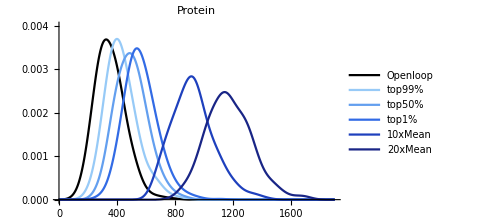

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hpgen1[[1]][[1]]/hpgen1[[1]][[6]],hpgen50[[1]][[1]]/hpgen50[[1]][[6]],hpgen99[[1]][[1]]/hpgen99[[1]][[6]],hpgen3000[[1]][[1]]/hpgen3000[[1]][[6]],hpgen6000[[1]][[1]]/hpgen6000[[1]][[6]]},50,PlotRange->{{0,1900},{0,0.004}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

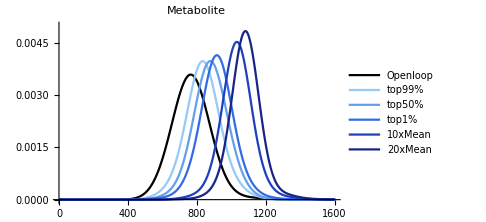

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hpgen1[[1]][[4]]/hpgen1[[1]][[6]],hpgen50[[1]][[4]]/hpgen50[[1]][[6]],hpgen99[[1]][[4]]/hpgen99[[1]][[6]],hpgen3000[[1]][[4]]/hpgen3000[[1]][[6]],hpgen6000[[1]][[4]]/hpgen6000[[1]][[6]]},70,PlotRange->{{0,1600},{0,0.005}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

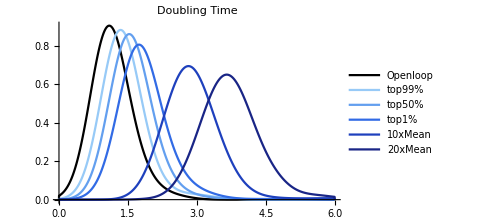

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hpgen1[[1]][[5]],Log[2]/hpgen50[[1]][[5]],Log[2]/hpgen99[[1]][[5]],Log[2]/hpgen3000[[1]][[5]],Log[2]/hpgen6000[[1]][[5]]},0.35,PlotRange->{{0,6},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hpmem3000=metabproteinmemfast[hpkeep3000];
```

```mathematica
hpmem6000=metabproteinmemfast[hpkeep6000];
```

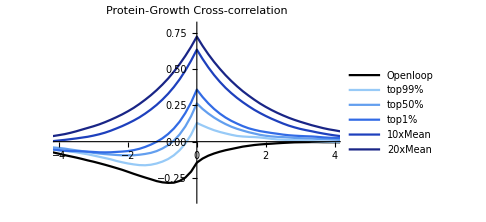

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hpmem1[[4]],hpmem50[[4]],hpmem99[[4]],hpmem3000[[4]],hpmem6000[[4]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

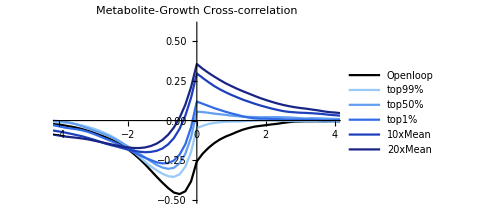

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hpmem1[[5]],hpmem50[[5]],hpmem99[[5]],hpmem3000[[5]],hpmem6000[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

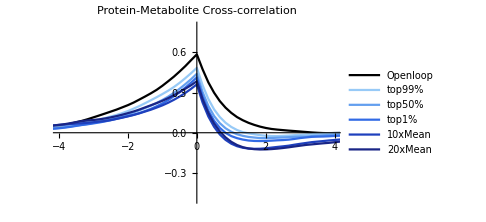

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hpmem1[[6]],hpmem50[[6]],hpmem99[[6]],hpmem3000[[6]],hpmem6000[[6]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

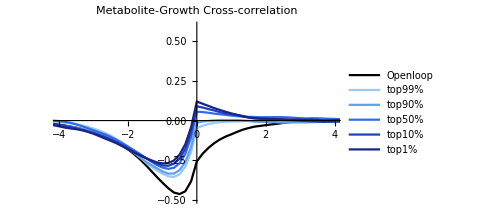

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hpmem1[[5]],hpmem10[[5]],hpmem50[[5]],hpmem90[[5]],hpmem99[[5]]},PlotRange->{{-4,4},{-0.5,0.6}},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%"},PlotLabel->Style["Metabolite-Growth Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#97caf7"],Thick],Directive[RGBColor["#639fef"],Thick],Directive[RGBColor["#326be5"],Thick],Directive[RGBColor["#1e40bd"],Thick],Directive[RGBColor["#192586"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

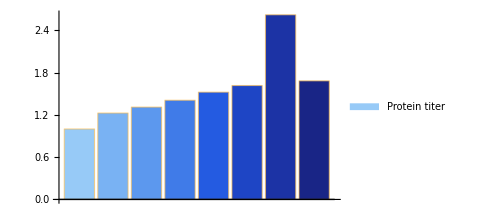

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hptyp1[[2]]/oltyp[[2]],hptyp10[[2]]/oltyp[[2]],hptyp50[[2]]/oltyp[[2]],hptyp90[[2]]/oltyp[[2]],hptyp99[[2]]/oltyp[[2]],hptyp3000[[2]]/oltyp[[2]],hptyp6000[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

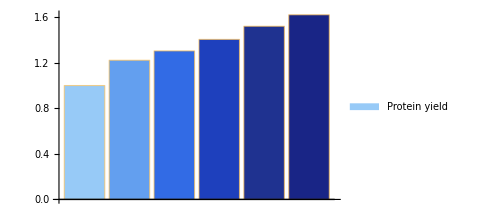

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hptyp1[[5]]/oltyp[[5]],hptyp10[[5]]/oltyp[[5]],hptyp50[[5]]/oltyp[[5]],hptyp90[[5]]/oltyp[[5]],hptyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

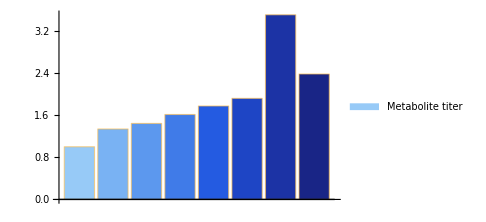

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hptyp1[[4]]/oltyp[[4]],hptyp10[[4]]/oltyp[[4]],hptyp50[[4]]/oltyp[[4]],hptyp90[[4]]/oltyp[[4]],hptyp99[[4]]/oltyp[[4]],hptyp3000[[4]]/oltyp[[4]],hptyp6000[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite titer"},ChartStyle->{RGBColor["#97caf7"],RGBColor["#79b2f3"],RGBColor["#5c98ee"],
RGBColor["#407be8"],
RGBColor["#245be1"],
RGBColor["#1e45c5"],
RGBColor["#1c33a5"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

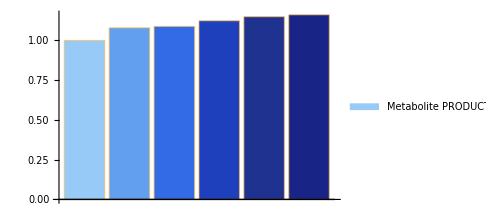

```mathematica
BarChart[{oltyp[[9]]/oltyp[[9]],hptyp1[[9]]/oltyp[[9]],hptyp10[[9]]/oltyp[[9]],hptyp50[[9]]/oltyp[[9]],hptyp90[[9]]/oltyp[[9]],hptyp99[[9]]/oltyp[[9]]},ChartLegends->{"Metabolite PRODUCTIVITY"},ChartStyle->{RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[1]],hptyp1[[1]],hptyp10[[1]],hptyp50[[1]],hptyp90[[1]],hptyp99[[1]],hptyp3000[[1]],hptyp6000[[1]]},PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","10xMean","20xMean"},PlotStyle->{Black,Lighter[RGBColor["#97caf7"]],RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],PlotLabel->"protein titer" ,
ImageSize->Medium]
```

-Graphics-

```mathematica
ListLinePlot[{oltyp[[3]],hptyp1[[3]],hptyp10[[3]],hptyp50[[3]],hptyp90[[3]],hptyp99[[3]],hptyp3000[[3]],hptyp6000[[3]]},PlotLabel->"metabolite titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","hp=10xmean","hp=20xmean"},PlotStyle->{Black,Lighter[RGBColor["#97caf7"]],RGBColor["#97caf7"],
RGBColor["#639fef"],
RGBColor["#326be5"],
RGBColor["#1e40bd"],
RGBColor["#1f3290"],
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

-Graphics-